Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

```mathematica
gghaa=(GetYodaRaw[NotebookDirectory[]<>"gghaa.yoda"]);
```

2 Imported ..Histo1D..  /ATLAS_1408_7084/forward_lowpt/0

1 Imported ..Histo1D..  /ATLAS_1408_7084/central_highpt/0

3 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta_inc/0

2 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta/0

1 Imported ..Histo1D..  /ATLAS_1407_5063/Mee/0

This contains Hist1D objects:

OptionValue::nodef: Unknown option "PlotStyle" for HistogramPlot.

Rescaling Histogram y-Axis with 0.125

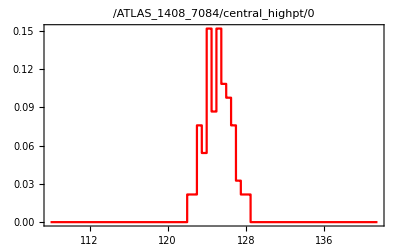

```mathematica
F1=HistogramPlot[gghaa[[1]],HistScale->0.15/1.2,PlotStyle->{Red}]
```

```mathematica
ATLAS1=(GetYodaRaw[NotebookDirectory[]<>"ATLAS_gghaa_central_high.yoda"]);
```

1 Imported ..Scatter2D..  /REF/ATLAS_1008_2461/d01-x01-y01

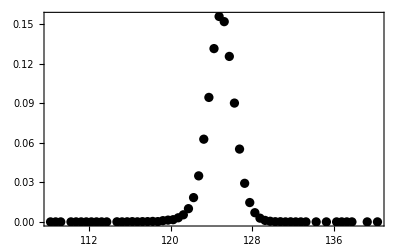

```mathematica
F2=ScatterPlot[ATLAS1[[1]],PlotStyle->{Black}]
```

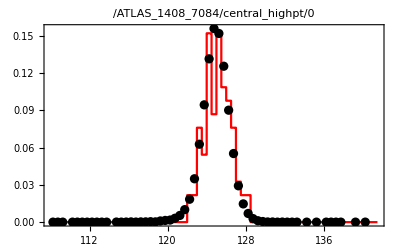

```mathematica
Show[{F1,F2}]
```

OptionValue::nodef: Unknown option "PlotStyle" for HistogramPlot.

Rescaling Histogram y-Axis with 0.025

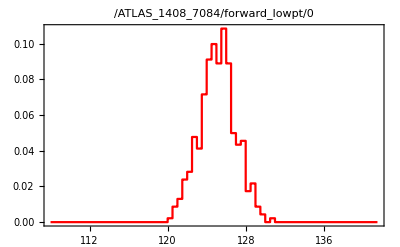

```mathematica
G1=HistogramPlot[gghaa[[2]],HistScale->0.15/6,PlotStyle->{Red}]
```

1 Imported ..Scatter2D..  /REF/ATLAS_1008_2461/d01-x01-y01

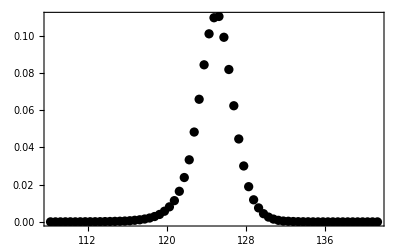

```mathematica
ATLAS2=(GetYodaRaw[NotebookDirectory[]<>"ATLAS_gghaa_forward_low.yoda"]);
G2=ScatterPlot[ATLAS2[[1]],PlotStyle->{Black}]
```

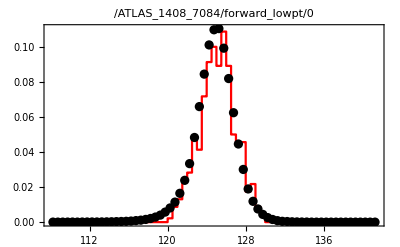

```mathematica
Show[G1,G2]
```